# Bipartite entanglement harvesting with multiple detectors

```mathematica
(*Define Mathematica notebook style and settings*)
If[Length@PacletFind["MaTeX"]==0,ResourceFunction["MaTeXInstall"][]];
If[!MemberQ[$Packages,"MaTeX`"],<<MaTeX`];
fontSize=12;
SetOptions[MaTeX,FontSize->fontSize];
SetOptions[Plot,BaseStyle->{FontSize->fontSize,FontFamily->"Latin Modern Math"}];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"];

imageFolderPath="<placeholder>"(*Enter a folder path where images are saved*);
```

## Switching and smearing functions

### Exact forms of the switching and smearing functions in momentum space

```mathematica
(*Define Gaussian smearing and switching functions in momentum space*)
sFuncMomGaussian[k_, σ_] := Exp[-1/2 k^2 σ^2] (*With corresponding spatial version in n dimensions: 1/((2 Pi σ^2)^(n/2))exp(-r^2/(2 σ^2))*);
```

```mathematica
(*Define compactly supported (CS) smearing and switching functions in momentum space with the exact forms*)
smearingMomCompactifiedPolynomial[k_,R_,δ_]:=Hypergeometric0F1[5/2+δ,-1/4 k^2 R^2](*Compactified (1-r^2/R^2)^δ in 3D*);
switchingMomCompactifiedPolynomial[ω_,T_,δ_]:=Hypergeometric0F1[3/2+δ,-1/4 T^2 ω^2](*Compactified (1-t^2/T^2)^δ in 1D*);
```

```mathematica
switchingMomGaussianTruncated[ω_,σ_,T_] :=Re[ 1/2 ⅇ^(-1/2 σ^2 ω^2) (Erf[(T-ⅈ σ^2 ω)/(√2 σ)]+Erf[(T+ⅈ σ^2 ω)/(√2 σ)])];
switchingMomCos2[ω_,T_]:=(1/T)(Sin[ω T]/ω+1/2 (Sin[(ω-π/T) T]/(ω-π/T)+Sin[(ω+π/T) T]/(ω+π/T)))(*switchingSpatCos2[t_,T_]:=Piecewise[{{(1/T)Cos[Pi t/(2 T)]^2,Abs[t]<=T}},0];*);
switchingMomSech2[ω_,ρ_]:=Piecewise[{{1,ω==0}},(Pi ρ ω)/(2 Sinh[Pi ρ ω/2])];
```

### Extra: more on the switching and smearing functions

```mathematica
(*Derivation of the exact compactly supported smearing and switching functions*)
h[q_,R_,δ_]:=(1-q^2/R^2)^δ;
hNormalizationConstant3D[R_,δ_]:=1/Integrate[4 π r^2 h[r,R,δ],{r,0,R}];
hNormalizationConstant1D[T_,δ_]:=1/Integrate[h[t,T,δ],{t,-T,T}];
smearingFuncSpatCS[r_,R_,δ_]:=hNormalizationConstant3D[R,δ] h[r,R,δ] (*smearing function in spatial space wo/ compactification*);
switchingFuncSpatCS[t_,T_,δ_]:=hNormalizationConstant1D[T,δ] h[t,T,δ](*switching function in spatial space wo/ compactification*); 
smearingFuncMomCS[k_,R_,δ_]:=Assuming[{R>0,δ>1},(4 π/k) Integrate[smearingFuncSpatCS[r,R,δ] Sin[k r] r,{r,0,R}]](*compactified smearing function in momentum space*);
switchingFuncMomCS[ω_,T_,δ_]:=Assuming[{T>0,δ>1},Integrate[switchingFuncSpatCS[t,T,δ] Exp[-ⅈ ω t],{t,-T,T}]](*compactified switching function in momentum space*);
(*Print the results*)
Print[smearingFuncMomCS[k,R,δ]];
Print[switchingFuncMomCS[ω,T,δ]];
```

Hypergeometric0F1[5/2+δ,-1/4 k^2 R^2]

Hypergeometric0F1[3/2+δ,-1/4 T^2 ω^2]

```mathematica
(*Define bump function in 1D*)
bumpNormFactor[T_]:=bumpNormFactor[T]=NIntegrate[Exp[1/((t/T)^2-1)],{t,-T,T},Method->"GaussKronrodRule"];
integrandNorm=Compile[
{{t,_Real},{ω,_Real},{T,_Real},{norm,_Real}},
Exp[1/((t/T)^2-1)]/norm*Cos[ω t],
CompilationTarget->"C",RuntimeOptions->"Speed"
];
bump1DMom[ω_,T_]:=Module[{norm,integrand},
norm=bumpNormFactor[T];
integrand[t_?NumericQ]:=integrandNorm[t,ω,T,norm];
2 NIntegrate[integrand[t],{t,0,T},Method->"GaussKronrodRule"]
];
```

```mathematica
(*Define a version of the Gaussian smearing/switching which has been compactified by cutting the tails => compactified between [-R,R]*)
sFuncMomGaussianTruncated[k_,σ_,R_] := 1/2 ⅇ^(-1/2 σ^2 k^2) (Erf[(R-ⅈ σ^2 k)/(√2 σ)]+Erf[(R+ⅈ σ^2 k)/(√2 σ)]);
(*Plateau bumb function*)
h[u_]:=If[u<=0.,0.,Exp[-1./u]];
smoothStep[x_]:=Which[x<=0.,0.,x>=1.,1.,True,h[x]/(h[x]+h[1.-x])];
switchingSpatPlateauRaw[t_,a_,T_]:=Module[{at=Abs[t]},Which[at<=a,1.,at>=T,0.,True,smoothStep[(T-at)/(T-a)]]];
switchingSpatPlateauNorm[a_,T_]:=switchingSpatPlateauNorm[a,T]=NIntegrate[switchingSpatPlateauRaw[s,a,T],{s,-T,T},Method->"GaussKronrodRule"];
switchingMomPlateau[ω_,a_,T_]:=Module[{norm=switchingSpatPlateauNorm[a,T],plateau,edge,integrand},
plateau=If[Abs[ω]<10.^-14,2. a,2. Sin[ω a]/ω];
integrand[t_?NumericQ]:=switchingSpatPlateauRaw[t,a,T]*Cos[ω t];
edge=2. NIntegrate[integrand[t],{t,a,T},Method->"GaussKronrodRule"];
(plateau+edge)/norm
];
```

### Extra: plot switching functions

```mathematica
RtExample=0.01 (*Half-width of the interaction time window (also denoted T)*);

(*Define switching functions in spatial space*)
switchingSpatGaussian[t_,σ_]:=Exp[-t^2/(2 σ^2)]/Sqrt[2Pi σ^2];
switchingSpatGaussianTruncated[t_,σ_,T_]:=Piecewise[{{Exp[-t^2/(2 σ^2)]/Sqrt[2Pi σ^2],Abs[t]<=T}},0];
switchingSpatCompactifiedPolynomial[t_,T_,δ_]:=Piecewise[{{(1-t^2/T^2)^δ/(T Sqrt[Pi] Gamma[δ+1]/Gamma[δ+3/2]),Abs[t]<=T}},0];
switchingSpatCos2[t_,T_]:=Piecewise[{{(1/T)Cos[Pi t/(2 T)]^2,Abs[t]<=T}},0];
switchingSpatSech2[t_,ρ_]:=Sech[t/ρ]^2/(2 ρ);

(*Plot switching functions in spatial space*)
Plot[
{
switchingSpatGaussian[t,RtExample/5],
switchingSpatGaussianTruncated[t,RtExample/5,RtExample],
switchingSpatCompactifiedPolynomial[t,RtExample,2.00001],
switchingSpatCompactifiedPolynomial[t,RtExample,9.4],
switchingSpatCompactifiedPolynomial[t,RtExample,20.00001]
},
{t,-1.5 RtExample,1.5 RtExample},
Frame->True,GridLines->Automatic,
FrameLabel->{MaTeX["t"],MaTeX["\\chi(t)"]},
PlotStyle->{{Blue},{Red,Dashed},{Opacity[.8]},{Orange,Opacity[.8]},{Opacity[.8]}},
PlotLegends->{
MaTeX["\\text{Gaussian }(T=5\\sigma)"],
MaTeX["\\text{Truncated Gaussian }(T=5\\sigma)"],
MaTeX["\\text{Compactified polynomial }(\\delta=2.0)"],
MaTeX["\\text{Compactified polynomial }(\\delta=9.4)"],
MaTeX["\\text{Compactified polynomial }(\\delta=20.0)"]
},
PlotPoints->100,
ImageSize->400
]
(*Plot switching functions in momentum space*)
Plot[
{
sFuncMomGaussian[ω,RtExample/5],
switchingMomGaussianTruncated[ω,RtExample/5,RtExample],
switchingMomCompactifiedPolynomial[ω,RtExample,2.00001],
switchingMomCompactifiedPolynomial[ω,RtExample,9.4],
switchingMomCompactifiedPolynomial[ω,RtExample,20.00001],
switchingMomInterpBump[ω]
},
{ω,-30/RtExample,30/RtExample},
Frame->True,GridLines->Automatic,
FrameLabel->{MaTeX["\\omega"],MaTeX["\\tilde\\chi(\\omega)"]},
PlotStyle->{{Blue},{Red,Dashed},{Opacity[.8]},{Orange,Opacity[.8]},{Opacity[.8]}},
PlotLegends->{
MaTeX["\\text{Gaussian }(T=5\\sigma)"],
MaTeX["\\text{Truncated Gaussian }(T=5\\sigma)"],
MaTeX["\\text{Compactified polynomial }(\\delta=2.0)"],
MaTeX["\\text{Compactified polynomial }(\\delta=9.4)"],
MaTeX["\\text{Compactified polynomial }(\\delta=20.0)"]
},
PlotRange->{All,All},
ImageSize->400
]
```

## Define the setup (needs user input)

Note: when changing the setup parameters in the following cell, such as the switching function, it is a good practice to run all the initialization cells

```mathematica
(* ================================================================*)
(*USER SETUP BEGINS: define numerical constants, smearing and switching*)
prec=30 (*Working precision for all numerical computations; 30 is enough*);
Rt1=SetPrecision[1/100,prec];(*Half-width of the interaction time window (also denoted T)*);
(*Rs1=Rt1/20(*Detector spatial size; only required for non-pointlike detectors*);*)
α1=5(*Dimensionless scale factor controlling approximate compact support in non-compact support cases such as Gaussian*); 
smearingMom[k_]:=1(*some options: smearingFuncMomCSGeneral[k,Rs1,3] or sFuncMomGaussian[k, Rs1/α1] or 1 (if point-like)*);
switchingMom[ω_]:=sFuncMomGaussian[ω,Rt1/α1](*some options: sFuncMomGaussian[ω,Rt1/α1], switchingMomGaussianTruncated[ω,Rt1/α1,Rt1], switchingMomCompactifiedPolynomial[ω,Rt1,9.4] or 1 (if point-like)*);
(*USER SETUP ENDS*)
(* ================================================================*)

(*Define configuration flags and numerical parameters*)
isPointlikeDetectors=(smearingMom[1.5Rt1] == 1);
isGaussianSwitching=(switchingMom[1.5Rt1]==Simplify[sFuncMomGaussian[1.5Rt1, Rt1/α1]]);
If[!isPointlikeDetectors&&!NumericQ[Rs1],MessageDialog["Error: Rs1 must be defined as a numerical value when not using pointlike detectors."];Abort[]];
ΔT=2Rt1 (*Total interaction time window*);
L1=If[isPointlikeDetectors, ΔT,2 Rs1+ΔT](*Minimal causal separation l*);
kmin1=0(*Numerical integration minimum; should be zero*);
kmax1=200/L1(*Numerical integration maximum (cut-off); approx 200/system_size is enough for most setups*);

(*Define the integrands of the reduced density matrix components*)
PiiIntegrand[k_,Ω_]:=k/(4 π^2) Abs[smearingMom[k]]^2 Abs[switchingMom[k+Ω]]^2(*also denoted P*);
CijIntegrand[k_,Δx_,Ω_]:=1/(4 π^2 Δx)  Sin[k Δx] Abs[smearingMom[k]]^2switchingMom[k+Ω]^2(*also denoted C_ij*);
XijPlusIntegrand[k_,Δx_,Ω_]:=-(1/(4 π^2 Δx))Sin[k Δx] Abs[smearingMom[k]]^2  (switchingMom[k+Ω] switchingMom[k-Ω])(*also denoted X_ij*);

(*Define the reduced density matrix components*)
If[isPointlikeDetectors && isGaussianSwitching,
Print["Using closed forms for Cij and Xij terms since we have Gaussian switching and point-like detectors..."];
Pii[Ω_]:=(Exp[-(σ Ω)^2]-Sqrt[Pi] σ Ω Erfc[σ Ω])/(8(Pi σ)^2)/. σ->Rt1/α1;
Cij[Δx_,Ω_]:=If[Δx==0,Pii[Ω],Exp[−(Δx/(2 σ))^2]/(8 π^(3/2) Δx σ)*(Re[Exp[−ⅈ Δx Ω]Erfi[Δx/(2 σ)+ⅈ σ Ω]]-Sin[Δx Ω])/. σ->Rt1/α1];
CijPlus[Δx_,Ω_]:=Re[(Exp[−(Δx/(2 σ))^2-ⅈ Δx Ω](Exp[2ⅈ Δx Ω] Erfi[Δx/(2 σ)-ⅈ σ Ω]+Erfi[Δx/(2 σ)+ⅈ σ Ω]))/(16 Pi^(3/2)Δx σ)]/. σ->Rt1/α1;
CijMinus[Δx_,Ω_]:=-(Exp[−(Δx/(2 σ))^2] Sin[Δx Ω])/(8 Pi^(3/2) Δx σ)/. σ->Rt1/α1;
XijPlus[Δx_,Ω_]:=-(Exp[−(σ Ω)^2] DawsonF[Δx/(2 σ)])/(4 Pi^2 Δx σ)/. σ->Rt1/α1;
XijMinus[Δx_,Ω_]:=(ⅈ Exp[−(Δx/(2 σ))^2-(σ Ω)^2])/(8 Pi^(3/2) Δx σ)/. σ->Rt1/α1;
Xij[Δx_,Ω_]:=XijPlus[Δx,Ω]+XijMinus[Δx,Ω];
,
Print["Using numerical integrals for Cij and Xij terms..."];
Pii[Ω_]:=NIntegrate[PiiIntegrand[k,Ω],{k,kmin1,kmax1}, Method->"Oscillatory", AccuracyGoal->25];
Cij[Δx_,Ω_]:=If[Δx==0,Pii[Ω],NIntegrate[CijIntegrand[k,Δx,Ω],{k,kmin1,kmax1}, Method->"Oscillatory", AccuracyGoal->25]];
XijPlus[Δx_,Ω_]:=NIntegrate[XijPlusIntegrand[k,Δx,Ω],{k,kmin1,kmax1},Method->"Oscillatory", AccuracyGoal->25];(*Method->"Oscillatory",AccuracyGoal->25*)
];
```

Using closed forms for Cij and Xij terms since we have Gaussian switching and point-like detectors...

### Derive the closed forms of the reduced density matrix components in Gaussian switching and point-like detectors case

```mathematica
(*Compute analytically matrix components with Gaussian switching and point-like detectors*)
PiiIntegrandGaussianAndPointlike[k_,Ω_,σ_]:=k/(4 π^2)  sFuncMomGaussian[k+Ω,σ]^2;
CijIntegrandGaussianAndPointlike[k_,Δx_,Ω_,σ_]:=1/(4 π^2 Δx)  Sin[k Δx] sFuncMomGaussian[k+Ω,σ]^2;
CijPlusIntegrandGaussianAndPointlike[k_,Δx_,Ω_,σ_]:=1/(4 π^2 Δx)  Sin[k Δx] (1/2 sFuncMomGaussian[k+Ω,σ]^2 + 1/2 sFuncMomGaussian[k-Ω,σ]^2);
CijMinusIntegrandGaussianAndPointlike[k_,Δx_,Ω_,σ_]:=1/(4 π^2 Δx)  Sin[k Δx] (1/2 sFuncMomGaussian[k+Ω,σ]^2 - 1/2 sFuncMomGaussian[k-Ω,σ]^2);
XijPlusIntegrandGaussianAndPointlike[k_,Δx_,Ω_,σ_]:=-(1/(4 π^2 Δx))Sin[k Δx]  (sFuncMomGaussian[k+Ω,σ] sFuncMomGaussian[k-Ω,σ]);
XijMinusIntegrandGaussianAndPointlike[k_,Δx_,Ω_,τ_,σ_]:=ⅈ/((2π)^3Δx τ)Sin[k Δx]  (sFuncMomGaussian[k-Ω-τ,σ]sFuncMomGaussian[k+Ω-τ,σ] -sFuncMomGaussian[k+Ω+τ,σ] sFuncMomGaussian[k-Ω+τ,σ]);
(*Get the analytical expressions of the matrix components*)
Print["Pii = \n",Assuming[{Ω>0,σ>0,Δx>0},Integrate[PiiIntegrandGaussianAndPointlike[k,Ω,σ],{k,0,Infinity}]]];

Print["Cij = \n",Assuming[{Ω>0,σ>0,Δx>0},Integrate[CijIntegrandGaussianAndPointlike[k,Δx,Ω,σ],{k,0,Infinity}]]](*output = Exp[−(Δx/(2 σ))^2]/(8 π^(3/2) Δx σ)*(Re[Exp[−ⅈ Δx Ω]Erfi[Δx/(2 σ)+ⅈ σ Ω]]-Sin[Δx Ω])*)
Print["Cij+ = \n",Assuming[{Ω>0,σ>0,Δx>0},Integrate[CijPlusIntegrandGaussianAndPointlike[k,Δx,Ω,σ],{k,0,Infinity}]]]
Print["Cij- = \n",Assuming[{Ω>0,σ>0,Δx>0},Integrate[CijMinusIntegrandGaussianAndPointlike[k,Δx,Ω,σ],{k,0,Infinity}]]]
Print["Xij+ = \n",Assuming[{Ω>0,σ>0,Δx>0},Integrate[XijPlusIntegrandGaussianAndPointlike[k,Δx,Ω,σ],{k,0,Infinity}]]]
Print["Xij- = \n",Assuming[{Ω>0,σ>0,Δx>0},Integrate[XijMinusIntegrandGaussianAndPointlike[k,Δx,Ω,τ,σ],{τ,-Infinity,Infinity},{k,0,Infinity}]]]
```

Lii = 
(ⅇ^(-σ^2 Ω^2)-√π σ Ω Erfc[σ Ω])/(8 π^2 σ^2)

Lij = 
(ⅇ^(-1/4 Δx (Δx/σ^2+4 ⅈ Ω)) (-ⅈ+ⅇ^(2 ⅈ Δx Ω) (ⅈ+Erfi[Δx/(2 σ)-ⅈ σ Ω])+Erfi[Δx/(2 σ)+ⅈ σ Ω]))/(16 π^(3/2) Δx σ)

Lij+ = 
(ⅇ^(-1/4 Δx (Δx/σ^2+4 ⅈ Ω)) (ⅇ^(2 ⅈ Δx Ω) Erfi[Δx/(2 σ)-ⅈ σ Ω]+Erfi[Δx/(2 σ)+ⅈ σ Ω]))/(16 π^(3/2) Δx σ)

Lij- = 
-(ⅇ^(-Δx^2/(4 σ^2)) Sin[Δx Ω])/(8 π^(3/2) Δx σ)

Mij+ = 
-(ⅇ^(-σ^2 Ω^2) DawsonF[Δx/(2 σ)])/(4 π^2 Δx σ)

Mij- = 
(ⅈ ⅇ^(-(Δx^2+4 σ^4 Ω^2)/(4 σ^2)))/(8 π^(3/2) Δx σ)

```mathematica
(*=> 2 detector LO negativity*)
Print["Neg(2 detectors) = ",Abs[-(ⅇ^(-σ^2 Ω^2) DawsonF[Δx/(2 σ)])/(4 π^2 Δx σ)+(ⅈ ⅇ^(-(Δx^2+4 σ^4 Ω^2)/(4 σ^2)))/(8 π^(3/2) Δx σ)]-(ⅇ^(-σ^2 Ω^2)-√π σ Ω Erfc[σ Ω])/(8 π^2 σ^2)]
```

Neg(2 detectors) = Abs[(ⅈ ⅇ^(-(Δx^2+4 σ^4 Ω^2)/(4 σ^2)))/(8 π^(3/2) Δx σ)-(ⅇ^(-σ^2 Ω^2) DawsonF[Δx/(2 σ)])/(4 π^2 Δx σ)]-(ⅇ^(-σ^2 Ω^2)-√π σ Ω Erfc[σ Ω])/(8 π^2 σ^2)

### Analysis of Gaussian causal contact on the matrix components

#### Define the plotting function for C-/C

```mathematica
plotXOmegaContourPlot[dataTable_,xLabel_:"x",zLabel_:"\\mathcal{N}^{(2)}",contourVals_:Range[-18,18,2],threshold_:1*^-14,shouldExport_:False]:=Module[
{minVal,maxVal,zeroPlane,plot3D,plotContour,yMin,yMax},

minVal=Min[dataTable[[All,3]]];
maxVal=Max[dataTable[[All,3]]];
yMin=Min[dataTable[[All,2]]];
yMax=Max[dataTable[[All,2]]];

plotContour=ListContourPlot[
dataTable,
InterpolationOrder->2,
Contours->contourVals,
(*ContourLabels->(Function[{z,xy},Text[Style[NumberForm[z,{4,2}],FontSize->10,Bold,Background->White],xy]]),*)
FrameLabel->{MaTeX[StringTemplate["``/L"][xLabel]],MaTeX["\\Omega T"]},
PlotLegends->BarLegend[Automatic,LegendLabel->Placed[MaTeX[zLabel],Above]],
PlotRange->{All,All,All},
AspectRatio->0.7,
ColorFunction->Function[z,If[z<=threshold,Gray,ColorData["Rainbow"][Rescale[z,{minVal,maxVal}]]]],
ColorFunctionScaling->False,
MaxPlotPoints->300,
ImageSize->400,
GridLines->Automatic,
Epilog->{Thick,Dashed,Black,Line[{{1.0,yMin},{1.0,yMax}}]}
];

Print["Plot maximum around: ", MaximalBy[dataTable,#[[3]]&][[1]]];

If[shouldExport,
(
Export[FileNameJoin[{imageFolderPath,"C_plot.pdf"}],Rasterize[plotContour,ImageResolution->600],ImageSize->Large];
)
];

plotContour
]
```

#### Plot

```mathematica
sampleΩ=Subdivide[1/Rt1,31/Rt1,200];
sampleX=Subdivide[0.5L1,1.5L1,200];
dataCijLogAbsRelDiff=Join@@ParallelTable[{r/L1,Ω Rt1,Log10[Abs[CijMinus[r,Ω]/Cij[r,Ω]]]},{r,sampleX}, {Ω,sampleΩ}];
```

```mathematica
plotXOmegaContourPlot[dataCijLogAbsRelDiff,"x_{ij}","\\log_{10}\\Bigg|\\frac{C_{ij}^-}{C_{ij}}\\Bigg|",Range[-20,16,4],-30,True]
```

Plot maximum around: {0.52,31.,15.2182}

```mathematica
dataXijLogAbsRelDiff=Table[{r/L1,Log10[Abs[XijMinus[r,0]/Xij[r,0]]]},{r,Subdivide[0.5L1,1.5L1,1000]}];
XijPlot=ListPlot[
{dataXijLogAbsRelDiff},
Joined->True,Frame->True,ImageSize->400,PlotRange->{All,All},FrameLabel->{MaTeX["x_{ij}/L"],None},
PlotStyle->{{Blue,Opacity[.75]}},
PlotLegends->MaTeX["\\log_{10}\\Bigg|\\frac{X_{ij}^-}{X_{ij}}\\Bigg|"],
Epilog->{Thick,Dashed,Black,Line[{{1.0,0},{1.0,-30}}]},GridLines->Automatic
]
Export[FileNameJoin[{imageFolderPath,"X_plot.pdf"}],Rasterize[XijPlot,ImageResolution->600],ImageSize->Large];
```

### Analysis of energy gap on the matrix components

```mathematica
LUsed=L1;
sampleΩ=Subdivide[0.1/Rt1,37/Rt1,250];

dataPii=ParallelTable[{Ω Rt1,Pii[Ω]},{Ω,sampleΩ}];
dataXijPlus=ParallelTable[{Ω Rt1,XijPlus[LUsed,Ω]},{Ω,sampleΩ}];
(*
dataCijSqrt2=ParallelTable[{Ω Rt1,Cij[Sqrt[2]LUsed,Ω]},{Ω,sampleΩ}];
dataCij2=ParallelTable[{Ω Rt1,Cij[2LUsed,Ω]},{Ω,sampleΩ}];
dataCij1=ParallelTable[{Ω Rt1,Cij[LUsed,Ω]},{Ω,sampleΩ}];
dataCijPlus1=ParallelTable[{Ω Rt1,CijPlus[LUsed,Ω]},{Ω,sampleΩ}];
dataCijMinus1=ParallelTable[{Ω Rt1,CijMinus[LUsed,Ω]},{Ω,sampleΩ}];
*)

diff=Abs[dataXijPlus[[All,2]]]-dataPii[[All,2]];
Ωlines=dataPii[[All,1]][[Flatten@Position[Partition[Sign[diff],2,1],{x_,y_}/;x y<0]]];
nonZeroHarvestingRegimes={Directive[Dashed],Opacity[.3],Line/@({{#,-20},{#,10^3}}&/@Ωlines)};
Print["Non-zero two-detector harvesting somewhere: ", AnyTrue[diff,#>0&]]
```

Non-zero two-detector harvesting somewhere: False

```mathematica
(*Switch to Gaussian and compute for comparison*)
sampleΩ=Subdivide[0.1/Rt1,37/Rt1,1000](*Enter sampleΩ*);
{dataGaussianPii,dataGaussianXij,dataGaussianXijPlus,dataGaussianCijSqrt2,dataGaussianCij2}=Block[
{isGaussianSwitching,isPointlikeDetectors,Pii,Cij,Xij,XijPlus,XijMinus},
{isGaussianSwitching,isPointlikeDetectors}={True,True};
Pii[Ω_]:=(Exp[-(σ Ω)^2]-Sqrt[Pi] σ Ω Erfc[σ Ω])/(8(Pi σ)^2)/. σ->Rt1/α1;
Xij[Δx_,Ω_]:=(-(Exp[−(σ Ω)^2] DawsonF[Δx/(2 σ)])/(4 Pi^2 Δx σ)+(ⅈ Exp[−(Δx/(2 σ))^2-(σ Ω)^2])/(8 Pi^(3/2) Δx σ))/. σ->Rt1/α1;
Cij[Δx_,Ω_]:=If[Δx==0,Pii[Ω],Exp[−(Δx/(2 σ))^2]/(8 π^(3/2) Δx σ)*(Re[Exp[−ⅈ Δx Ω]Erfi[Δx/(2 σ)+ⅈ σ Ω]]-Sin[Δx Ω])/. σ->Rt1/α1];
XijPlus[Δx_,Ω_]:=-(Exp[−(σ Ω)^2] DawsonF[Δx/(2 σ)])/(4 Pi^2 Δx σ)/. σ->Rt1/α1;
XijMinus[Δx_,Ω_]:=(ⅈ Exp[−(Δx/(2 σ))^2-(σ Ω)^2])/(8 Pi^(3/2) Δx σ)/. σ->Rt1/α1;
{
Table[{Ω Rt1,Pii[Ω]},{Ω,sampleΩ}],
Table[{Ω Rt1,Xij[L1,Ω]},{Ω,sampleΩ}],
Table[{Ω Rt1,XijPlus[L1,Ω]},{Ω,sampleΩ}],
Table[{Ω Rt1,Cij[Sqrt[2] L1,Ω]},{Ω,sampleΩ}],
Table[{Ω Rt1,Cij[2 L1,Ω]},{Ω,sampleΩ}]
}
];
diffGaussian=Abs[dataGaussianXijPlus[[All,2]]]-dataGaussianPii[[All,2]];
ΩlinesGaussian=dataGaussianPii[[All,1]][[Flatten@Position[Partition[Sign[diffGaussian],2,1],{x_,y_}/;x y<0]]];
nonZeroHarvestingGaussianRegimes=Line/@({{#,-20},{#,10^3}}&/@ΩlinesGaussian);
```

```mathematica
elementsLogPlot=ListPlot[
{
{#[[1]],Log10[#[[2]]]}&/@dataGaussianPii,
{#[[1]],Log10[#[[2]]]}&/@dataPii,
{#[[1]],Log10[Abs[#[[2]]]]}&/@dataGaussianXijPlus,
{#[[1]],Log10[Abs[#[[2]]]]}&/@dataXijPlus
(*{#[[1]],Log10[Abs[#[[2]]]]}&/@dataCij1,
{#[[1]],Log10[Abs[#[[2]]]]}&/@dataCijPlus1,
{#[[1]],Log10[Abs[#[[2]]]]}&/@dataCijMinus1*)(*,
{#[[1]],Log10[Abs[#[[2]]]]}&/@dataGaussianCijSqrt2,
{#[[1]],Log10[Abs[#[[2]]]]}&/@dataCijSqrt2,
{#[[1]],Log10[Abs[#[[2]]]]}&/@dataGaussianCij2,
{#[[1]],Log10[Abs[#[[2]]]]}&/@dataCij2*)
},
PlotStyle->{{Blue,Opacity[.75]},{Blue,Dashed,Opacity[.75]},{Orange,Opacity[.75]},{Orange,Dashed,Opacity[.75]},{Darker[Green],Dashed,Opacity[.75]},{Purple,Dashed,Opacity[.75]},{Darker[Green],Opacity[.75]},{Darker[Green],Dashed,Opacity[.75]},{Purple,Opacity[.75]},{Purple,Dashed,Opacity[.75]}},
Frame->True,Axes->False,PlotMarkers->None,Joined->True,ImageSize->400,
PlotRange->{{0,36},{-15,5}},
FrameLabel->{MaTeX["\\Omega T"],None},
GridLines->{Range[0,37,5],Range[-15,5,5]},
PlotLegends->{
MaTeX["\\log_{10}(P)\\text{ with Gaussian switching}"],
MaTeX["\\log_{10}(P)\\text{ with truncated Gaussian switching}"],
MaTeX["\\log_{10}|X(x/L=1)|\\text{ with Gaussian switching}"],
MaTeX["\\log_{10}|X(x/L=1)|\\text{ with truncated Gaussian switching}"]
},
Prolog->Module[{g=Sort@N[ΩlinesGaussian],makePairs,ymin=-15,ymax=5},
makePairs[xs_]:=Module[{y=xs},If[OddQ@Length@y,y=Append[y,40]];Partition[y,2,2]];
Flatten@{
If[Length@makePairs[g]>0,Join[{Gray,Opacity[0.20]},(Rectangle@@@({{#[[1]],ymin},{#[[2]],ymax}}&/@makePairs[g]))],{}]
}
]
]
```

```mathematica
Export[FileNameJoin[{imageFolderPath,"elements_plot_g_truncated.pdf"}],Rasterize[elementsLogPlot,ImageResolution->600],ImageSize->Large];
```

### Test how the matrix elements integrands behave with momentum

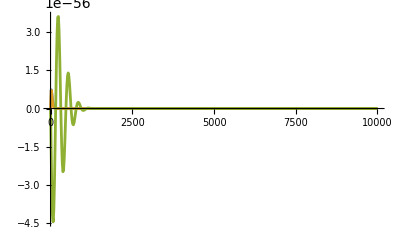

```mathematica
(*Set the energy gap*)
ΩTest=SetPrecision[56.49315/Rt1,prec](*Optimal 2-detector energy gap: Gaussian=24.49315/Rt1, CP94=??*);

(*Plot L and M integrands wrt momentum*)
sampleK=Subdivide[0,200/l1,500];
dataPiiIntegrand=Table[{k,PiiIntegrand[k,ΩTest]},{k,sampleK}];
dataCijIntegrand=Table[{k,CijIntegrand[k,l1,ΩTest]},{k,sampleK}];
dataXijIntegrand=Table[{k,XijPlusIntegrand[k,l1,ΩTest]},{k,sampleK}];
(*dataMijMinusIntegrand=Table[{k,( ⅇ^(-(Rt1/α1)^2 (k^2+ΩTest^2)) Erfi[k (Rt1/α1)] Sin[k l1])/(4 π^2 l1)},{k,sampleK}];*)
ListPlot[
{dataPiiIntegrand,dataCijIntegrand,dataXijIntegrand},
Joined->True,PlotRange->{All,All},AxesLabel->{MaTeX["k"],None},
PlotLegends->{MaTeX["P_{ii,\\text{ integrand}}(k)"],MaTeX["C_{ij,\\text{ integrand}}(k)"],MaTeX["X_{ij,\\text{ integrand}}^+(k)"]}
]
```

## Define general plotting functions

### Define a general distance--Ω plotting function (3D and contour)

```mathematica
plotXOmegaPlots[dataTable_,xLabel_:"x",zLabel_:"\\mathcal{N}^{(2)}",contourCount_:12,threshold_:1*^-14,shouldExport_:False]:=Module[
{minX,maxX,minΩ,maxΩ,minVal,maxVal,zeroPlane,plot3D,plotContour},

minX=Min[dataTable[[All,1]]];
maxX=Max[dataTable[[All,1]]];
minΩ=Min[dataTable[[All,2]]];
maxΩ=Max[dataTable[[All,2]]];
minVal=Min[dataTable[[All,3]]];
maxVal=Max[dataTable[[All,3]]];

(*3D plot with zero plane*)
zeroPlane=Graphics3D[{Opacity[1],Gray,Polygon[{{minX,minΩ,threshold},{maxX,minΩ,threshold},{maxX,maxΩ,threshold},{minX,maxΩ,threshold}}]}];
plot3D=Show[ListPlot3D[
dataTable,
InterpolationOrder->2,
AxesLabel->{MaTeX[StringTemplate["``/L"][xLabel]],MaTeX["\\Omega T"],MaTeX[zLabel]},
ColorFunction->"Rainbow",
PlotRange->{All,All,All},
ImageSize->400,
AspectRatio->0.7,
ViewPoint->{3.096,-1.131,0.766}
],
zeroPlane
];

plotContour=ListContourPlot[
dataTable,
InterpolationOrder->2,
Contours->Subdivide[threshold,Max[dataTable[[All,3]]],contourCount],
FrameLabel->{MaTeX[StringTemplate["``/L"][xLabel]],MaTeX["\\Omega T"]},
PlotLegends->BarLegend[Automatic,LegendLabel->Placed[MaTeX[zLabel],Above]],
PlotRange->{All,All,All}(*Gaussian option:{{1,maxX/l1},All,All}*),
AspectRatio->0.7,
ColorFunction->Function[z,If[z<=threshold,Gray,ColorData["Rainbow"][Rescale[z,{minVal,maxVal}]]]],
ColorFunctionScaling->False,
MaxPlotPoints->300,
ImageSize->400,
GridLines->None
];

Print["Plot maximum around: ", MaximalBy[dataTable,#[[3]]&][[1]]];

If[shouldExport,
(
Export[FileNameJoin[{imageFolderPath,"surface_plot.pdf"}],Rasterize[plot3D,ImageResolution->600],ImageSize->Large];
Export[FileNameJoin[{imageFolderPath,"contour_plot.pdf.pdf"}],Rasterize[plotContour,ImageResolution->600],ImageSize->Large];
)
];

GraphicsGrid[{{plot3D},{plotContour}}](*Return all plots in a column layout*)
]
```

### Define a general 3 detector arrangement plotting function

```mathematica
plotGeneral3DetectorPlots[dataTable_,plotRange_:{{-4,4},{-4,4},All},contourCount_:14,threshold_:1*^-14,shouldExport_:False, shouldPlotOnlyDensity_:False]:=Module[
{dataCartesian,dataUpper,dataLower,dataFull,minVal,maxVal,zeroPlane,plot2D,plot3D,plotContour},

(*Convert polar coordinates to Cartesian*)
dataCartesian=dataTable/. {r_,thetaPi_,val_}:>{r Cos[thetaPi Pi],r Sin[thetaPi Pi],val};
dataUpper=Select[dataCartesian,#[[2]]>=0&];
dataLower=dataUpper/. {x_,y_,v_}:>{x,-y,v};
dataFull=Join[dataUpper,dataLower];

(*Create 2D density plot with central disk*)
plot2D=Show[
ListDensityPlot[
dataFull,
(*InterpolationOrder->2,*)
PlotLegends->BarLegend[Automatic,LegendLabel->Placed[MaTeX["\\mathcal{N}^{(2)}"],Above]],
ColorFunction->Function[z,If[z<=threshold,Gray,ColorData["Rainbow"][Rescale[z,{Min[dataTable[[All,3]]],Max[dataTable[[All,3]]]}]]]],
ColorFunctionScaling->False,
FrameLabel->{MaTeX["q_1 / L"],MaTeX["q_2 / L"]},
PlotRange->plotRange,
AspectRatio->1,
ImageSize->400,
RegionFunction->Function[{x,y,z},Sqrt[x^2+y^2]>=dataFull[[1,1]]]
],
Graphics[{White,Disk[{0,0},dataFull[[1,1]]]}],
Sequence@@If[dataFull[[1,1]]<1,{Graphics[{White,Opacity[.5],Circle[{0,0},1]}]},{}](*Show causal disconnection circle if plotting inner circle also*)
];

(*Exit module early if only plotting density*)
If[shouldPlotOnlyDensity,
If[shouldExport,Export[FileNameJoin[{imageFolderPath,"3detectors_density.pdf"}],Rasterize[plot2D,ImageResolution->600],ImageSize->Large]];
Return[plot2D]
];

(*Create surface plot with zero plane*)
zeroPlane=Graphics3D[{Opacity[1],Gray,Polygon[{{1,0,threshold/100},{plotRange[[1]][[2]],0,threshold/100},{plotRange[[1]][[2]],1,threshold/100},{1,1,threshold/100}}]}];
plot3D=Show[
ListPlot3D[
dataTable,
InterpolationOrder->2,
AxesLabel->{MaTeX["r/L"],MaTeX["\\theta/\\pi"],MaTeX["\\mathcal{N}^{(2)}"]},
ColorFunction->"Rainbow",
PlotRange->{{1,plotRange[[1]][[2]]},All,All},
ImageSize->400,
AspectRatio->0.7
],
zeroPlane
];

(*Create contour plot in polar coordinates*)
plotContour=ListContourPlot[
dataTable,
InterpolationOrder->2,
Contours->Subdivide[threshold,Max[dataTable[[All,3]]],contourCount],
FrameLabel->{MaTeX["r/L"],MaTeX["\\theta/\\pi"]},
PlotLegends->BarLegend[Automatic,LegendLabel->Placed[MaTeX["\\mathcal{N}^{(2)}"],Above]],
PlotRange->{{1,plotRange[[1]][[2]]},All,All},
AspectRatio->0.7,
ColorFunction->Function[z,If[z<=threshold,Gray,ColorData["Rainbow"][Rescale[z,{Min[dataTable[[All,3]]],Max[dataTable[[All,3]]]}]]]],
ColorFunctionScaling->False,
ImageSize->400,
GridLines->None
];

If[shouldExport,
(
Export[FileNameJoin[{imageFolderPath,"3detectors_density.pdf"}],Rasterize[plot2D,ImageResolution->600],ImageSize->Large];
Export[FileNameJoin[{imageFolderPath,"3detectors_3d.pdf"}],Rasterize[plot3D,ImageResolution->600],ImageSize->Large];
Export[FileNameJoin[{imageFolderPath,"3detectors_contour.pdf"}],Rasterize[plotContour,ImageResolution->600],ImageSize->Large];
)
];

Row[{plot2D,plot3D,plotContour}]
]
```

## Two detectors

### Define the LO negativity function

```mathematica
neg2GaussianAnalytExpWithOnlyXPlus[Δx_,Ω_,σ_]:=Max[0,Exp[-σ^2 Ω^2]/(8 π^2 Δx σ^2)(2 σ DawsonF[Δx/(2 σ)]+Δx (-1+ⅇ^(σ^2 Ω^2) √π σ Ω Erfc[σ Ω]))](*Derived in previous cells using X~X+*);
neg2GaussianAnalytExpExact[Δx_,Ω_,σ_]:=Max[0,Abs[Xij[Δx,Ω]]-Pii[Ω]];
neg2Detectors[x_,Ω_]:=If[isGaussianSwitching && isPointlikeDetectors, neg2GaussianAnalytExpExact[x,Ω,Rt1/α1],Max[0,Abs[XijPlus[x,Ω]]-Pii[Ω]]];
```

#### Extra analysis on approximate negativity N+ with two detectors

```mathematica
diffNeg[x_,Ω_]:=Module[
{precX=SetPrecision[x,30],precΩ=SetPrecision[Ω,30],absXij,absXijPlus,piiVal,diff},
absXij=Abs[Xij[precX,precΩ]];
absXijPlus=Abs[XijPlus[precX,precΩ]];
piiVal=Pii[precΩ];
diff=absXij-piiVal;
If[diff>0,(absXij-absXijPlus)/diff,0]
];
diffNegAtL[Ω_]:=Module[
{precX=SetPrecision[L1,30],precΩ=SetPrecision[Ω,30],absXij,absXijPlus,piiVal,diff},
absXij=Abs[Xij[precX,precΩ]];
absXijPlus=Abs[XijPlus[precX,precΩ]];
piiVal=Pii[precΩ];
diff=absXij-piiVal;
If[diff>0,(absXij-absXijPlus)/diff,0]
];
```

```mathematica
sampleΩ=Subdivide[23.5/Rt1,26/Rt1,1000]; 
diffDataNeg2AtL=Table[{Ω Rt1,diffNegAtL[Ω]},{Ω,sampleΩ}];
```

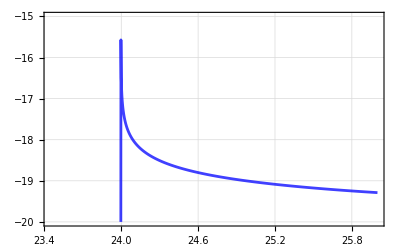

```mathematica
ListPlot[
{{#[[1]],Log10[If[#[[2]]==0,10^-30,#[[2]]]]}&/@diffDataNeg2AtL},
Joined->True,PlotMarkers->None,PlotRange->{All,{-20,-15}},Frame->True,
FrameLabel->{MaTeX["\\Omega T"],MaTeX["\\log_{10}|(\\mathcal{N}-\\mathcal{N}^{+})/\\mathcal{N}|"]},
ImageSize->400,
GridLines->Automatic,
PlotStyle->{{Blue,Opacity[.75]},{Orange,Opacity[.75], Dashed},{Darker[Green],Opacity[.75]},{Red,Opacity[.75]},{Purple,Opacity[.75]}}
]
```

```mathematica
{sampleX,sampleΩ}={
Subdivide[0.8L1,1.1L1,100],
Subdivide[23.5/Rt1,26/Rt1,100]
}; 
diffNegData=Join@@ParallelTable[{r/L1,Ω Rt1,diffNeg[r,Ω]},{r,sampleX}, {Ω,sampleΩ}];
```

```mathematica
plotXOmegaPlots[diffNegData,"x","\\mathcal{N}^{(2)}",12,1*^-30,False]
```

Plot maximum around: {0.8,23.5,8.6685795425743×10^-13}

### Plot LO negativity varying both separation and energy levels

```mathematica
{sampleX,sampleΩ}=If[
isGaussianSwitching&&isPointlikeDetectors,
{
Subdivide[L1,1.1L1,200],
Subdivide[23/Rt1,28/Rt1,200]
},
 {
Subdivide[L1,1.4L1,10](*Enter sampleX*),
Subdivide[11/Rt1,14/Rt1,10](*Enter sampleΩ, CS94:[11/Rt1,14/Rt1,10]*)
}
]; 
{sampleX2,sampleΩ2}={Subdivide[L1,1.15L1,10],Subdivide[15.0/Rt1,18/Rt1,10]}; 
{sampleX3,sampleΩ3}={Subdivide[L1,1.05L1,10],Subdivide[19.5/Rt1,21.5/Rt1,10]}; 

dataNeg2XOmega=Join@@ParallelTable[{r/L1,Ω Rt1,neg2Detectors[r,Ω]},{r,sampleX}, {Ω,sampleΩ}];
plotXOmegaPlots[dataNeg2XOmega,"x","\\mathcal{N}^{(2)}",12,1*^-14,True]
```

Plot maximum around: {1.,24.5,9.28289×10^-11}

### Compute the precise maximum of LO negativity

```mathematica
minΩ=If[isGaussianSwitching && isPointlikeDetectors,24.4931/Rt1,11.86/Rt1];
maxΩ=If[isGaussianSwitching && isPointlikeDetectors,24.4932/Rt1,11.87/Rt1];
sampleΩ=Subdivide[minΩ,maxΩ,1000]; 
dataNeg2Precise=Table[{Ω Rt1,neg2Detectors[L1,Ω]},{Ω,sampleΩ}];
omegaMax2=First[dataNeg2Precise[[First[Ordering[dataNeg2Precise[[All,2]],-1]]]]]/Rt1;
Print["Precise optimal Ω = ",omegaMax2];
Print["Precise optimal (Ω,N) = ",dataNeg2Precise[[First[Ordering[dataNeg2Precise[[All,2]],-1]]]]];
```

$Aborted

Precise optimal Ω = 2449.31

Precise optimal (Ω,N) = {24.4931,9.28379×10^-11}

### Extra: plot the LO negativity varying only the energy gap (with minimal separation)

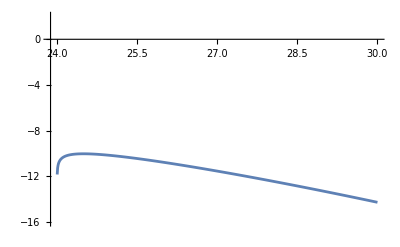

```mathematica
sampleΩ=If[
isGaussianSwitching&&isPointlikeDetectors,
Subdivide[22/Rt1,30/Rt1,1000],
Subdivide[4.5/Rt1,6.2/Rt1,50]
];
dataNeg2Log10=ParallelTable[{Ω Rt1,Log10[neg2Detectors[L1,Ω]]},{Ω,sampleΩ}];

ListPlot[
{dataNeg2Log10},
Joined->True,
PlotRange->{All, {-16,2}},
ImageSize->400,
AxesLabel->{MaTeX["\\Omega T"],MaTeX["\\log_{10}\\mathcal{N}^{(2)}"]}
]
```

### Set the optimal 2 - detector energy gap Ω2

```mathematica
Ω2=If[isGaussianSwitching && isPointlikeDetectors,SetPrecision[24.4931496826/Rt1,prec],SetPrecision[ΩOpt,prec]](*Gaussian&PL value computed with 10^6 datapoints in [24.4931/Rt1,24.4932/Rt1]]*);
```

## Three detectors AA|B

### Define 3 detector LO negativity analytically

```mathematica
(*Define LO negativity function where one detector position is given in polar coordinates*)
neg3Detectors[Ω_,r_,θ_,l_:L1]:=Module[{P,Xl,Xr,x,Cx,S,R,ρ,ϕ,eigenvals,negativity},
P=Pii[Ω];
Xl=If[isGaussianSwitching&&isPointlikeDetectors,Xij[l,Ω],XijPlus[l,Ω]](*Use complex value of Mij when there is no compact support*);
Xr=If[isGaussianSwitching&&isPointlikeDetectors,Xij[r,Ω],XijPlus[r,Ω]](*Use complex value of Mij when there is no compact support*);
x=Sqrt[r^2+l^2-2r l Cos[θ]];
Cx=If[x/l<1*^-7 ,Pii[Ω],Cij[x,Ω]];
S=Sqrt[Abs[Cx]^2+Abs[Xr]^2+Abs[Xl]^2];
R=Re[Cx Xr Conjugate[Xl]];
ρ=Sqrt[4/3]S;
ϕ=(1/3) ArcCos[3 Sqrt[3] R/S^3];
eigenvals=Table[P+ρ Cos[ϕ+2 Pi (k-1)/3],{k,1,3}];
negativity=Total[-Select[eigenvals,#<0&]];
negativity
];

(*Define a table version of neg3Detectors*)
negTable3Detectors[Ω_,sampleR_:Range[L1,3.4L1,0.01L1],sampleθ_:Range[0,Pi,Pi/128],l_:L1]:=Join@@ParallelTable[
{r/l,θ/π,neg3Detectors[Ω,r,θ,l]},
{r,sampleR},
{θ,sampleθ}
];
```

### Extra: study interesting cases analytically by printing extra info about the parameters

```mathematica
print3DetectorInfo[r_,θ_,Ω_,l_:L1]:=Module[
{P,Cx,CxPlus,CxMinus,Xl,Xr,x,S,R,ρ,ϕ,eigenvals,negativity},

P=Pii[Ω];
Xl=Xij[l,Ω];
Xr=Xij[r,Ω];
x=Sqrt[r^2+l^2-2r l Cos[θ]];
Cx=Cij[x,Ω];
CxPlus=CijPlus[x,Ω];
CxMinus=CijMinus[x,Ω];
S=Sqrt[Abs[Cx]^2+Abs[Xr]^2+Abs[Xl]^2];
R=Re[Cx Xr Conjugate[Xl]];
ρ=Sqrt[4/3]S;
ϕ=(1/3) ArcCos[3 Sqrt[3] R/S^3];

Print["Analytical results with r/l=",r/l,", θ=",θ,", Ω=",Ω,":"];
Print["x/l = ", x/l];
Print["P = ", P];
Print["C = ", Cx];
Print["C+ = ", CxPlus];
Print["C- = ", CxMinus];

Print[""];
Print["X^2 < P/2(P+C) : ", Abs[Xl]^2 < P/2(P+Cx)];
Print["X^2 > P^2/3(1+2C/P) : ", Abs[Xl]^2 > P^2/3(1+2Cx/P)];
Print["X^2 > P^2/4 : ",  Abs[Xl]^2>P^2/4];
Print[""];
Print["ρ/P = ", ρ/P];
Print["ϕ = ",ϕ/Pi,"π = π/",Pi/ϕ];
Print["Cos(ϕ1) = ", Cos[ϕ]];
Print["Cos(ϕ2) = ", Cos[ϕ+2Pi/3]];
Print["Cos(ϕ3) = ", Cos[ϕ+4Pi/3]];
Print["α1 = ", P+ρ Cos[ϕ]];
Print["α2 = ", P+ρ Cos[ϕ+2 Pi (2-1)/3]];
Print["α3 = ", P+ρ Cos[ϕ+2 Pi (3-1)/3]];

eigenvals=Table[P+ρ Cos[ϕ+2 Pi (k-1)/3],{k,1,3}];
negativity=Total[-Select[eigenvals,#<0&]];
Print["LO negativity = ",negativity];
Print["--------------------------"];
negativity
];
```

```mathematica
(*USE THIS CELL TO PRINT THE INTERESTING CASES*)

print3DetectorInfo[l1,Pi,Ω2](*ABA case with optimal two-detector energy gap*);
print3DetectorInfo[l1,Pi,2131](*ABA case with optimal energy gap*);
print3DetectorInfo[1.115499 l1,0,20.60/Rt1](*ABB case with optimal energy gap*);
```

### Plot general 3 detector case with specific energy gap

```mathematica
(*Evaluate*)
ΩUsed=Ω2(*Enter energy gap, e.g. optimal two-detector energy gap Ω2, 21.362/Rt1*);
Print["Computing with ΩT = ",ΩUsed Rt1," ..."];
negData3Detectors=negTable3Detectors[ΩUsed,Range[1L1,3.4L1,0.02L1],Range[0,Pi,Pi/128]];
Print["Maximum at: ",MaximalBy[negData3Detectors,#[[3]]&][[1]]];
```

Computing with ΩT = 24.49314968259999659494496882 ...

$Aborted

Maximum at: {1.,1,8.74079×10^-10}

```mathematica
(*Plot*)
plotGeneral3DetectorPlots[negData3Detectors,{{-2.3,2.3},{-2.3,2.3},All},14,1*^-14,False,True]
```

Min-Max values in the data: {9.28379×10^-11,8.74079×10^-10}

### Extra: generate density plot animation frames (as PNG’s) varying the energy gap

```mathematica
minΩ=19/Rt1;
maxΩ=30/Rt1;
omegaStep=0.05/Rt1;
Module[{i,Ω,negData3Detectors,densityPlot},
i=1;
Ω=minΩ;
While[Ω<=maxΩ,
negData3Detectors=negTable3Detectors[Ω,Range[1L1,3.4L1,0.02L1],Range[0,Pi,Pi/128]];
densityPlot=plotGeneral3DetectorPlots[negData3Detectors,{{-2.3,2.3},{-2.3,2.3},All},14,1*^-14,False,True];
Export[FileNameJoin[{imageFolderPath,"/animations/three_detectors/frames/frame-"<>IntegerString[i,10,3]<>".png"}],densityPlot,ImageResolution->200];
i+=1;
Ω+=omegaStep;
];
];
```

### Define LO negativity functions for special cases of ABA and AAB arrangements

```mathematica
neg3ABA[ Ω_,l_:L1] := Max[0, -Pii[Ω] - 1/2 Cij[2l, Ω] + 1/2 Sqrt[8 (-XijPlus[l, Ω])^2 + Cij[2l, Ω]^2]](*Derived in another nb*);
neg3AAB[x_, Ω_,l_:L1] :=neg3Detectors[Ω,l+x,0,l];
```

### Find optimal ABA and AAB configuration parameters

#### Optimize ABA configuration

```mathematica
(*Compute to find the precise optimal config of the ABA arrangement*)
sampleΩ=If[
isGaussianSwitching&&isPointlikeDetectors,
Subdivide[21.307/Rt1,21.309/Rt1,10000],
 Subdivide[21.35/Rt1,21.8/Rt1,100](*Enter sampleΩ*)
];
dataNeg3ABAOmegaPrecise=Table[{Ω Rt1,neg3ABA[Ω]},{Ω,sampleΩ}];
{omegaTMax3ABAPrecise,valMax3ABAprecise}=First@MaximalBy[dataNeg3ABAOmegaPrecise,Last];
Print["Optimal ABA configuration (ΩT, N): ",{omegaTMax3ABAPrecise,valMax3ABAprecise}];
```

Optimal ABA configuration (ΩT, N): {21.3635,5.38027×10^-8}

#### Optimize AAB configuration

```mathematica
(*Compute to find the precise optimal config of the AAB arrangement*)
{sampleX,sampleΩ}=If[
isGaussianSwitching&&isPointlikeDetectors,
{
Subdivide[0.1154957 L1,0.1155000 L1,100],
Subdivide[20.597/Rt1,20.599/Rt1,100]
},
 {
Subdivide[0.13L1,0.14L1,50](*Enter sampleX*),
Subdivide[20.75/Rt1,20.85/Rt1,50](*Enter sampleΩ*)
}
];
dataNeg3AABOmegaPrecise=Join@@ParallelTable[{r/L1,Ω Rt1,neg3AAB[r,Ω]},{r,sampleX}, {Ω,sampleΩ}];
Print["Optimal AAB configuration (x/l, ΩT, N): ",dataNeg3AABOmegaPrecise[[First[Ordering[dataNeg3AABOmegaPrecise[[All,3]],-1]]]]];
```

Optimal AAB configuration (x/l, ΩT, N): {0.1316,20.79,6.45727×10^-9}

```mathematica
(*Plot AAB case wrt energy gap and separation x*)
{sampleX,sampleΩ}=If[
isGaussianSwitching&&isPointlikeDetectors,
{
Subdivide[0,1L1,100],
Subdivide[18/Rt1,26/Rt1,100]
},
 {
Subdivide[0,2.5L1,40](*Enter sampleX*),
Subdivide[10/Rt1,14.5/Rt1,40](*Enter sampleΩ*)
}
];
dataNeg3AABOmega=Join@@ParallelTable[{r/L1,Ω Rt1,neg3AAB[r,Ω]},{r,sampleX}, {Ω,sampleΩ}];
plotXOmegaPlots[dataNeg3AABOmega,"x",12,1*^-14,False]
```

Plot maximum around: {0.,11.9125,0.00869525}

## Four detectors AA|BB (symmetric partition)

### Define symmetric four detector LO negativity functions

```mathematica
(*Define LO negativity functions which are derived in another nb*)
neg4AABB[x_,Ω_,l_:L1]:=
Max[0,-Pii[Ω]+1/2 (XijPlus[l,Ω]+XijPlus[l+2x,Ω])+1/2 Sqrt[4 (Cij[x,Ω]-XijPlus[l+x,Ω])^2+(XijPlus[l+2x,Ω]-XijPlus[l,Ω])^2]]+Max[0,-Pii[Ω]+1/2 (XijPlus[l,Ω]+XijPlus[l+2x,Ω])-1/2 Sqrt[4 (Cij[x,Ω]-XijPlus[l+x,Ω])^2+(XijPlus[l+2x,Ω]-XijPlus[l,Ω])^2]]+Max[0,-Pii[Ω]-1/2 (XijPlus[l,Ω]+XijPlus[l+2x,Ω])+1/2 Sqrt[4 (Cij[x,Ω]+XijPlus[l+x,Ω])^2+(XijPlus[l+2x,Ω]-XijPlus[l,Ω])^2]]+Max[0,-Pii[Ω]-1/2 (XijPlus[l,Ω]+XijPlus[l+2x,Ω])-1/2 Sqrt[4 (Cij[x,Ω]+XijPlus[l+x,Ω])^2+(XijPlus[l+2x,Ω]-XijPlus[l,Ω])^2]];
neg4ABBA[x_,Ω_,l_:L1]:=
Max[0,-Pii[Ω]+1/2 (Cij[x,Ω]+Cij[x+2 l,Ω])+1/2 Sqrt[4 (XijPlus[l,Ω]-XijPlus[x+l,Ω])^2+(Cij[x,Ω]-Cij[x+2 l,Ω])^2]]+
Max[0,-Pii[Ω]+1/2 (Cij[x,Ω]+Cij[x+2 l,Ω])-1/2 Sqrt[4 (XijPlus[l,Ω]-XijPlus[x+l,Ω])^2+(Cij[x,Ω]-Cij[x+2 l,Ω])^2]]+
Max[0,-Pii[Ω]-1/2 (Cij[x,Ω]+Cij[x+2 l,Ω])+1/2 Sqrt[4 (XijPlus[l,Ω]+XijPlus[x+l,Ω])^2+(Cij[x,Ω]-Cij[x+2 l,Ω])^2]]+Max[0,-Pii[Ω]-1/2 (Cij[x,Ω]+Cij[x+2 l,Ω])-1/2 Sqrt[4 (XijPlus[l,Ω]+XijPlus[x+l,Ω])^2+(Cij[x,Ω]-Cij[x+2 l,Ω])^2]];
neg4ABAB[x_,Ω_,l_:L1]:=
Max[0,-Pii[Ω]+1/2 (XijPlus[x,Ω]+XijPlus[3x,Ω])+1/2 Sqrt[4 (Cij[2x,Ω]-XijPlus[x,Ω])^2+(XijPlus[x,Ω]-XijPlus[3x,Ω])^2]]+
Max[0,-Pii[Ω]+1/2 (XijPlus[x,Ω]+XijPlus[3x,Ω])-1/2 Sqrt[4 (Cij[2x,Ω]-XijPlus[x,Ω])^2+(XijPlus[x,Ω]-XijPlus[3x,Ω])^2]]+
Max[0,-Pii[Ω]-1/2 (XijPlus[x,Ω]+XijPlus[3x,Ω])+1/2 Sqrt[4 (Cij[2x,Ω]+XijPlus[x,Ω])^2+(XijPlus[x,Ω]-XijPlus[3x,Ω])^2]]+
Max[0,-Pii[Ω]-1/2 (XijPlus[x,Ω]+XijPlus[3x,Ω])-1/2 Sqrt[4 (Cij[2x,Ω]+XijPlus[x,Ω])^2+(XijPlus[x,Ω]-XijPlus[3x,Ω])^2]];
neg4Rectangle[x_,Ω_,l_:L1]:=
Max[0,-Pii[Ω]-Cij[x,Ω]-XijPlus[l,Ω]-XijPlus[Sqrt[l^2+x^2],Ω]]+
Max[0,-Pii[Ω]+Cij[x,Ω]-XijPlus[l,Ω]+XijPlus[Sqrt[l^2+x^2],Ω]](*omitted two trivially positive eigenvalues*);
neg4SkewedSquare[x_,Ω_,l_:L1]:=
Max[0,-Pii[Ω]-1/2 (Cij[x,Ω]+Cij[Sqrt[4l^2-x^2],Ω])+1/2 Sqrt[16XijPlus[l,Ω]^2+1/4(Cij[x,Ω]-Cij[Sqrt[4l^2-x^2],Ω])^2]](*omitted two trivially positive eigenvalues*);
neg4ModTetrahedron[x_,Ω_,l_:L1]:=Max[0,-Pii[Ω]-Cij[x,Ω]-2XijPlus[l,Ω]](*omitted two trivially positive eigenvalues*);
```

### Compute and plot the AABB case

```mathematica
(*Compute for plotting and plot*)
{sampleX,sampleΩ}=If[
isGaussianSwitching&&isPointlikeDetectors,
{
Subdivide[0,0.5L1,200],
Subdivide[14/Rt1,22/Rt1,200]
},
 {
Subdivide[0,L1,20](*Enter sampleX*),
Subdivide[8.8/Rt1,14.2/Rt1,20](*Enter sampleΩ*)
}
];
dataNeg4AABB=Join@@ParallelTable[{x/L1,Ω Rt1,neg4AABB[x,Ω]},{x,sampleX},{Ω,sampleΩ}];
plotXOmegaPlots[dataNeg4AABB,"x","\\mathcal{N}^{(2)}",12,1*^-15,True]
```

Plot maximum around: {0.0775,17.16,1.90404×10^-6}

```mathematica
(*Compute precisely to find exact maximum*)
{sampleX,sampleΩ}=If[
isGaussianSwitching&&isPointlikeDetectors,
{
Subdivide[0.0763 L1,0.0767L1,10],
Subdivide[17.13/Rt1,17.15/Rt1,10]
},
 {
Subdivide[None,None,None](*Enter sampleX*),
Subdivide[None,None,None](*Enter sampleΩ*)
}
];
dataNeg4AABBPrecise=Join@@ParallelTable[{x/L1,Ω Rt1,neg4AABB[x,Ω]},{x,sampleX},{Ω,sampleΩ}];
Print["Optimal AABB configuration (x/l, ΩT, N): ", dataNeg4AABBPrecise[[First[Ordering[dataNeg4AABBPrecise[[All,3]],-1]]]]]
```

### Compute and plot the ABBA case

```mathematica
{sampleX,sampleΩ}=If[
isGaussianSwitching&&isPointlikeDetectors,
{
Subdivide[0,0.8L1,200],
Subdivide[17/Rt1,25/Rt1,200]
},
 {
Subdivide[0,L1,15](*Enter sampleX*),
Subdivide[9.5/Rt1,15/Rt1,15](*Enter sampleΩ*)
}
];
dataNeg4ABBA=Join@@ParallelTable[{x/L1,Ω Rt1,neg4ABBA[x,Ω]},{x,sampleX},{Ω,sampleΩ}];
plotXOmegaPlots[dataNeg4ABBA,"x","\\mathcal{N}^{(2)}",12,1*^-14,True]
```

Plot maximum around: {0.124,19.56,7.96645×10^-8}

```mathematica
(*Find precisely a local maximum*)
{sampleX,sampleΩ}=If[
isGaussianSwitching&&isPointlikeDetectors,
{
Subdivide[0.1241 L1,0.1246L1,10],
Subdivide[19.57/Rt1,19.59/Rt1,10]
},
 {
Subdivide[None,None,None](*Enter sampleX*),
Subdivide[None,None,None](*Enter sampleΩ*)
}
];
dataNeg4ABBAPrecise1=Join@@ParallelTable[{x/L1,Ω Rt1,neg4ABBA[x,Ω]},{x,sampleX},{Ω,sampleΩ}];
Print["A local maximum of AABB configuration (x/l, ΩT, N): ",dataNeg4ABBAPrecise1[[First[Ordering[dataNeg4ABBAPrecise1[[All,3]],-1]]]]]

(*Find precisely a local maximum with x=0*)
sampleΩ=If[
isGaussianSwitching&&isPointlikeDetectors,
Subdivide[21.308/Rt1,21.310/Rt1,100],
 Subdivide[None,None,None](*Enter sampleΩ*)
];
dataNeg4ABBAPrecise2=Table[{Ω Rt1,neg4ABBA[0,Ω]},{Ω,sampleΩ}];
Print["A local maximum of AABB configuration with x=0 (ΩT, N): ",dataNeg4ABBAPrecise2[[First[Ordering[dataNeg4ABBAPrecise2[[All,2]],-1]]]]]
```

The global maximum of AABB configuration (x/l, ΩT, N): {0.12415,19.576,7.96923×10^-8}

A local maximum of AABB configuration with x=0 (ΩT, N): {21.3089,7.45073×10^-8}

### Compute and plot the ABAB case

```mathematica
{sampleX,sampleΩ}=If[
isGaussianSwitching&&isPointlikeDetectors,
{
Subdivide[L1,1.1L1,200],
Subdivide[19/Rt1,23/Rt1,200]
},
 {
Subdivide[L1,1.7L1,15](*Enter sampleX*),
Subdivide[10/Rt1,14.5/Rt1,15](*Enter sampleΩ*)
}
];
dataNeg4ABAB=Join@@ParallelTable[{x/L1,Ω Rt1,neg4ABAB[x,Ω]},{x,sampleX},{Ω,sampleΩ}];
plotXOmegaPlots[dataNeg4ABAB,"x","\\mathcal{N}^{(2)}",12,1*^-14,True]
```

Plot maximum around: {1.,20.18,4.29258×10^-7}

```mathematica
(*Find precisely the optimal energy gap with minimal spatial separation*)
sampleΩ=If[
isGaussianSwitching&&isPointlikeDetectors,
Subdivide[20.1881/Rt1,20.1883/Rt1,1000],
Subdivide[None,None,100](*Enter sampleΩ*)
];
dataNeg4ABABPrecise=Table[{Ω Rt1,neg4ABAB[L1,Ω]},{Ω,sampleΩ}];
Print["Optimal ABAB configuration (ΩT, N): ",dataNeg4ABABPrecise[[First[Ordering[dataNeg4ABABPrecise[[All,2]],-1]]]]]
```

Optimal ABAB configuration (ΩT, N): {20.1882,4.293×10^-7}

### Compute and plot the Rectangle case

```mathematica
{sampleX,sampleΩ}=If[
isGaussianSwitching&&isPointlikeDetectors,
{
Subdivide[0,3L1,300],
Subdivide[23/Rt1,27/Rt1,300]
},
 {
Subdivide[0,3L1,20](*Enter sampleX*),
Subdivide[10.5/Rt1,14.5/Rt1,20](*Enter sampleΩ*)
}
];
dataNeg4Rectangle=Join@@ParallelTable[{x/L1,Ω Rt1,neg4Rectangle[x,Ω]},{x,sampleX},{Ω,sampleΩ}];
plotXOmegaPlots[dataNeg4Rectangle,"x","\\mathcal{N}^{(2)}",12,1*^-14,True]
```

Plot maximum around: {0.55,24.493333333333333333333333333,1.85675714863354941×10^-10}

```mathematica
(*Comparison to two detector case*)
Abs[neg4Rectangle[0.5L1,Ω2]-2neg2Detectors[L1,Ω2]]<10*^-20
```

True

### Compute and plot the Skewed Square case

```mathematica
{sampleX,sampleΩ}=If[
isGaussianSwitching&&isPointlikeDetectors,
{
Subdivide[0,Sqrt[2]L1,300],
Subdivide[18/Rt1,24/Rt1,300]
},
 {
Subdivide[0,Sqrt[2]L1,15](*Enter sampleX*),
Subdivide[18/Rt1,20/Rt1,15](*Enter sampleΩ, CS94:[9.5/Rt1,15/Rt1]*)
}
];
dataNeg4SkewedSquare=Join@@ParallelTable[{x/L1,Ω Rt1,neg4SkewedSquare[x,Ω]},{x,sampleX},{Ω,sampleΩ}];
plotXOmegaPlots[dataNeg4SkewedSquare,"x","\\mathcal{N}^{(2)}",12,1*^-14,True]
```

Plot maximum around: {1.4142135623730950488016887242,19.16,2.742491112495086280268771×10^-6}

```mathematica
dataNeg4SkewedSquarePrecise=ParallelTable[{Sqrt[2],Ω Rt1,neg4SkewedSquare[Sqrt[2]L1,Ω]},{Ω,Subdivide[19.16/Rt1,19.19/Rt1,10000]}];
Print["Optimal skewed square configuration (x/l, ΩT, N): ", MaximalBy[dataNeg4SkewedSquarePrecise,#[[3]]&][[1]]];
```

Optimal skewed square configuration (x/l, ΩT, N): {√2,19.1735,2.58665×10^-6}

### Compute and plot the Modified Tetrahedron case

```mathematica
{sampleX,sampleΩ}=If[
isGaussianSwitching&&isPointlikeDetectors,
{
Subdivide[0,Sqrt[2]L1,300],
Subdivide[18/Rt1,24.1/Rt1,300]
},
 {
Subdivide[0,Sqrt[2]L1,15](*Enter sampleX*),
Subdivide[15/Rt1,25/Rt1,15](*Enter sampleΩ, CS94:[9.5/Rt1,15/Rt1]*)
}
];
dataNeg4ModTetrahedron=Join@@ParallelTable[{x/L1,Ω Rt1,neg4ModTetrahedron[x,Ω]},{x,sampleX},{Ω,sampleΩ}];
plotXOmegaPlots[dataNeg4ModTetrahedron,"x","\\mathcal{N}^{(2)}",12,1*^-14,True]
```

Plot maximum around: {1.4142135623730950488016887242,19.159,2.7425×10^-6}

## Four detectors AAA|B (asymmetric partition)

### Define the block and LO negativity function

```mathematica
tildeRho1Asymm4[P_,Xl_,C32_,C21_,C31_]:={
{P,Conjugate[Xl],Conjugate[Xl],Conjugate[Xl]},
{Xl,P,C32,C31},
{Xl,C32,P,C21},
{Xl,C31,C21,P}
};
neg4Asymm[Ω_,θ21_,θ32_,l_:L1]:=Module[
{P,x32,x31,x21,C32,C31,C21,Xl,neg},

(*Compute the separations between the detectors*)
x21=2l Sin[θ21/2];
x32=2l Sin[θ32/2];
x31=2l Sin[(2Pi-θ21-θ32)/2];

(*Compute the matrix components, note: P=L_ii, C_ij=L_ij and X_ij=M_ij*)
P=Pii[Ω];
Xl=Xij[l,Ω];
C21=Cij[x21,Ω];
C32=Cij[x32,Ω];
C31=Cij[x31,Ω];

neg=-Total[Select[Eigenvalues[tildeRho1Asymm4[P,Xl,C32,C21,C31]],#<0&]];
neg
]
```

### Plot LO negativity in equilateral arrangement wrt energy gap

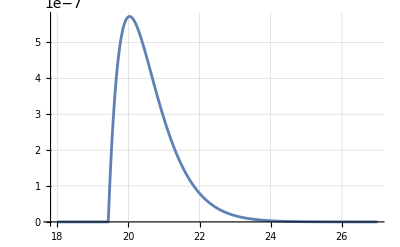

```mathematica
dataNeg4Asymm=ParallelTable[{Ω Rt1,neg4Asymm[Ω,2Pi/3,2Pi/3]},{Ω,1800,2700,0.1}]; 
comparisonLogPlot=ListPlot[
{dataNeg4Asymm},Joined->True,PlotMarkers->None,GridLines->Automatic
]
```

### Plot LO negativity in specific energy gap values wrt θ angles

```mathematica
(*Compute*)
dataNeg4AsymmVaryThetasOmega2=Join @@ParallelTable[{θ21/Pi,θ32/Pi,neg4Asymm[Ω2,θ21,θ32]},{θ21,Subdivide[0,2Pi,100]},{θ32,Subdivide[0.000000000000001,(2-1*^-15)Pi-θ21,100]}];
dataNeg4AsymmVaryThetasMax=Join @@ParallelTable[{θ21,θ32,neg4Asymm[2003.392,θ21,θ32]},{θ21,Subdivide[0,2Pi,100]},{θ32,Subdivide[0,2Pi-θ21,100]}];
```

```mathematica
(*Plot 3D surface plot*)
ListPlot3D[
dataNeg4AsymmVaryThetasOmega2,
InterpolationOrder->2,
AxesLabel->{MaTeX["\\theta_{21}/\\pi"],MaTeX["\\theta_{32}/\\pi"],MaTeX["\\mathcal{N}^{(2)}"]},
ColorFunction->"Rainbow",
ImageSize->400,
AspectRatio->0.7,
ViewPoint->{3.096,-1.131,0.766}
]

(*Plot contour plot*)
contourPlotAsymm=ListContourPlot[
dataNeg4AsymmVaryThetasOmega2,
InterpolationOrder->2,
Contours->4,
FrameLabel->{MaTeX["\\theta_{21}/\\pi"],MaTeX["\\theta_{32}/\\pi"]},
PlotLegends->BarLegend[Automatic,LegendLabel->Placed[MaTeX["\\mathcal{N}^{(2)}"],Above]],
PlotRange->{All,All,All},
ColorFunction->"Rainbow",
MaxPlotPoints->300,
ImageSize->300,
GridLines->None
]
```

## System size scale comparison

### Compute size scale data with specific energy level

```mathematica
ΩUsed=Ω2(*Enter the energy gap, for example Ω2*);
minL=ΔT;
maxL=1.6ΔT;
sampleL=Subdivide[minL,maxL,200];

dataNeg2=Table[{l/ΔT,neg2Detectors[l,ΩUsed]},{l,sampleL}];
dataNegABA=Table[{l/ΔT,neg3ABA[ΩUsed,l]},{l,sampleL}];
(*dataNegAAB=ParallelTable[{l/ΔT,neg3AAB[0.115499l,ΩUsed,l]},{l,sampleL}];*)
dataNegAABB=Table[{l/ΔT,neg4AABB[SetPrecision[0.07658 l,prec],ΩUsed,l]},{l,sampleL}];
(*dataNegABBA=Table[{l/ΔT,neg4ABBA[SetPrecision[0.124l,prec],ΩUsed,l]},{l,sampleL}];*)
dataNegABAB=Table[{l/ΔT,neg4ABAB[l,ΩUsed, l]},{l,sampleL}];
dataNegDiagonalSquare=Table[{l/ΔT,neg4ModTetrahedron[SetPrecision[Sqrt[2]l,prec],ΩUsed,l]},{l,sampleL}];
dataNeg4Asymm=Table[{l/ΔT,neg4Asymm[ΩUsed,2Pi/3,2Pi/3,l]},{l,sampleL}];
```

### Plot linearly and with log10

```mathematica
comparisonPlot=ListPlot[
{dataNeg2,dataNegABA,dataNegDiagonalSquare, dataNeg4Asymm,dataNegAABB},
Joined->True,PlotMarkers->None,PlotRange->All,Frame->True,
FrameLabel->{MaTeX["l/L"],MaTeX["\\mathcal{N}^{(2)}"]},
ImageSize->400,
GridLines->Automatic,
PlotStyle->{{Blue,Opacity[.75]},{Orange,Opacity[.75]},{Darker[Green],Opacity[.75]},{Red,Opacity[.75]},{Purple,Opacity[.75]}},
PlotLegends->Placed[
LineLegend[
{MaTeX["\\text{2-det}"],MaTeX["\\text{3-det: ABA}"],MaTeX["\\text{4-det: diagonal square}"],MaTeX["\\text{4-det: asymmetric}"],MaTeX["\\text{4-det: AABB}"]},
LegendFunction->(Framed[#,Background->White,FrameStyle->LightGray,RoundingRadius->3,FrameMargins->5]&)],
{0.76,0.65}
]
]
comparisonLogPlot=ListPlot[
{
{#[[1]],Log10[If[#[[2]]==0,10^-15,#[[2]]]]}&/@dataNeg2,
(*{#[[1]],Log10[If[#[[2]]==0,10^-15,#[[2]]]]}&/@dataNegAAB,*)
{#[[1]],Log10[If[#[[2]]==0,10^-15,#[[2]]]]}&/@dataNegABA,
(*{#[[1]],Log10[If[#[[2]]==0,10^-15,#[[2]]]]}&/@dataNegABBA,*)
{#[[1]],Log10[If[#[[2]]==0,10^-15,#[[2]]]]}&/@dataNegDiagonalSquare,
{#[[1]],Log10[If[#[[2]]==0,10^-15,#[[2]]]]}&/@dataNeg4Asymm,
{#[[1]],Log10[If[#[[2]]==0,10^-15,#[[2]]]]}&/@dataNegAABB
},
Joined->True,Frame->True,Axes->False,PlotMarkers->None,
PlotRange->{{1,1.75},{-12.5,-7.5}},
FrameLabel->{MaTeX["l/L"],MaTeX["\\log_{10}(\\mathcal{N}^{(2)})"]},
ImageSize->400,
GridLines->Automatic,
PlotStyle->{{Blue,Opacity[.75]},{Orange,Opacity[.75]},{Darker[Green],Opacity[.75]},{Red,Opacity[.75]},{Purple,Opacity[.75]}},
PlotLegends->Placed[
LineLegend[
{MaTeX["\\text{2-det}"],MaTeX["\\text{3-det: ABA}"],MaTeX["\\text{4-det: diagonal square}"],MaTeX["\\text{4-det: asymmetric}"],MaTeX["\\text{4-det: AABB }(x/l=0.08)"]},
LegendFunction->(Framed[#,Background->White,FrameStyle->LightGray,RoundingRadius->3,FrameMargins->5]&)],
{0.75,0.68}
]
]

(*Export[FileNameJoin[{imageFolderPath,"scale_comparison.pdf"}],Rasterize[comparisonPlot,ImageResolution->600],ImageSize->Large];*)
Export[FileNameJoin[{imageFolderPath,"scale_comparison_log10.pdf"}],Rasterize[comparisonLogPlot,ImageResolution->600],ImageSize->Large];
```

## Alternative linear chain (ABAB...)

### Define the general block, LO negativity and evaluation functions

```mathematica
(*Define the general  block as a function of the detector count*)
tildeRho1Chain[N_,Ω_,l_:L1]:=Module[
{nB,nA,maxL,Cvals,Xvals,kindex,elem},
nA=Ceiling[N/2](*# A detectors*);
nB=Floor[N/2](*# B detectors*);

Cvals=If[nA==1,{Pii[Ω]},Prepend[Table[Cij[2(k-1)l,Ω],{k,2,nA}],Pii[Ω]]];
Xvals=Table[Xij[(2k-1)l,Ω],{k,1,nB}];

kindex[r_,s_]:=Max[(r-nA)-s+1,s-(r-nA)];

elem[i_,j_]:=Which[
i<=nB&&j<=nB,Cvals[[Abs[i-j]+1]](*top left block element, C_BB*),
i>nB&&j>nB,Cvals[[Abs[i-j]+1]](*bottom right block element, C_AA*),
i>nB&&j<=nB,Xvals[[kindex[i,j]]](*bottom left block element, X_BA*),
True,Conjugate[elem[j,i]](*top right block element, (X_BA)^\dag*)
];

Table[elem[i,j],{i,1,N},{j,1,N}]
];

(*Define the LO negativity as the sum of the negaitive eigenvalues of *)
negChain[N_,Ω_,l_:L1]:=-Total[Select[Re@Eigenvalues[tildeRho1Chain[N,Ω,l]],#<0&]];

(*Define the table functions for evaluation and plotting*)
chainDataFuncDense[N_, l_:L1]:=Table[{Ω Rt1,negChain[N,Ω,l]},{Ω,1700,2600,1} ](*For dense evaluation*);
chainDataFuncCoarse[N_,l_:L1]:=Table[{Ω Rt1,negChain[N,Ω,l]},{Ω,1000,1400,10} ](*For coarse plotting*);
```

```mathematica
tildeRho1ChainV2[4,Ω,L] // MatrixForm
```

### Compute

```mathematica
(*Evaluate e.g. these*)
chainDataTablesDense5=Table[chainDataFuncDense[n],{n,2,5}];
```

```mathematica
chainDataTablesDense50=Table[chainDataFuncDense[n],{n,2,50}];
```

```mathematica
(*chainDataTablesScaled=Table[chainDataFuncCoarse[n,3.8ΔT],{n,2,20}];*)
```

### Analyse data directly

```mathematica
maxNegChainCoarse[N_,Ωmin_,Ωmax_,nPts_:10]:=Module[{grid},
grid=Subdivide[Ωmin,Ωmax,nPts];
MaximalBy[Table[{Ω,negChain[N,Ω,L1]},{Ω,grid}],Last]
];
maxNegChainCoarse[2,24.49/Rt1,25.00/Rt1,10000]
(*maxNegChainCoarse[600,18.88/Rt1,18.90/Rt1,10]*)
```

{{2449.32,9.28379×10^-11}}

### Plot

```mathematica
(*Enter the plotting parameters and the dataset name used*)
maxDetectors=50(*Enter how many detector data you want to show*);
dataSets=chainDataTablesDense50[[;;maxDetectors-1]](*Enter the data table variable name*);

(*Plot*)
maxPoints=Table[dataSets[[i]][[First@Ordering[dataSets[[i]][[All,2]],-1]]],{i,Length[dataSets]}];
theSmallMountain=ListPlot[
dataSets,
Frame->True,
Joined->True,Axes->True,AspectRatio->0.7,ImageSize->450,PlotRange->{{17.3,25.0},{All,All}}(*{{17.3,25.0},{All,All}}*),
FrameLabel->{MaTeX["\\Omega T"],MaTeX["\\mathcal{N}^{(2)}"]},
GridLines->{{18.88,24.49},{}},GridLinesStyle->Directive[GrayLevel[0.7],AbsoluteThickness[1.5]],
PlotStyle->Table[Directive[ColorData["Rainbow"][i/(maxDetectors-2)],Thickness[0.002]],{i,0,maxDetectors-2}],
PlotLegends->Placed[LineLegend[
{ColorData["Rainbow"][0/(maxDetectors-2)],ColorData["Rainbow"][1/(maxDetectors-2)],ColorData["Rainbow"][2/(maxDetectors-2)],White,ColorData["Rainbow"][(maxDetectors-2)/(maxDetectors-2)] },{MaTeX["\\text{2 detectors}"],MaTeX["\\text{3 detectors}"],MaTeX["\\text{4 detectors}"],MaTeX["\\vdots"],MaTeX[ToString[maxDetectors]<>"\\text{ detectors}"]},
LegendLayout->"Column"],
{0.68,0.7}
]
];
theSmallMountain=Show[
theSmallMountain,
ListPlot[maxPoints,PlotStyle->Directive[Gray,Opacity[0.8]],PlotMarkers->{"●",7} ]
]
Export[FileNameJoin[{imageFolderPath,"detector_chain_"<>ToString[maxDetectors]<>".pdf"}],Rasterize[theSmallMountain,ImageResolution->600],ImageSize->Large];
```

### Analyse and fit specific energy levels

```mathematica
dataTableForLinearFit=chainDataTablesDense50;
maxes=Table[MaximalBy[dataTableForLinearFit[[j]],#[[2]]&][[1]][[1]],{j,-1,-20,-1}];
Print["Plot average max (of last 20 curves) is at: ", Mean[maxes]];
```

Plot average max (of last 20 curves) is at: 18.9215

```mathematica
(*Double check the indices used*)
If [(dataTableForLinearFit[[1]][[189]][[1]]==18.88)&&(dataTableForLinearFit[[1]][[750]][[1]]==24.49), Print["Indices ok!"], Print["Error with indices!"]]
```

Indices ok!

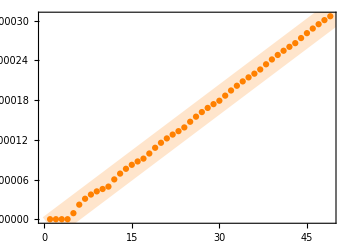

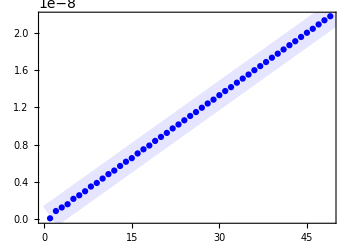

```mathematica
index1=189;  (*corresponding to ΩT=18.88*)
index2=750;  (*corresponding to ΩT=24.49*)

negsWithOmega1=Table[{i,dataTableForLinearFit[[i]][[index1]][[2]]},{i,1,Length[dataTableForLinearFit]}];
negsWithOmega2=Table[{i,dataTableForLinearFit[[i]][[index2]][[2]]},{i,1,Length[dataTableForLinearFit]}];

(*Fit linearly with least squares method*)
fit1=Fit[negsWithOmega1,{1,x},x];
fit2=Fit[negsWithOmega2,{1,x},x];

coeffs1=Association[CoefficientRules[fit1,x]];
coeffs2=Association[CoefficientRules[fit2,x]];

a1=coeffs1[{0}];
b1=coeffs1[{1}];
a2=coeffs2[{0}];
b2=coeffs2[{1}];

(*Rewrite fits in terms of (n-2):a+b n= b(n-2)+(a+2b)*)
newIntercept1=a1+2 b1;
newIntercept2=a2+2 b2;

(*Helper function to convert numbers to LaTeX scientific notation*)
toTeXScientific[num_]:=Module[{mantissa,exp},
{mantissa,exp}=MantissaExponent[num];
StringTemplate["``\\cdot 10^{``}"][NumberForm[mantissa,{3,2}],exp]
]
eqn1=MaTeX[StringTemplate["(``) (N - 2)  ``"][toTeXScientific[b1],toTeXScientific[newIntercept1]]];
eqn2=MaTeX[StringTemplate["(``) (N - 2) + ``"][toTeXScientific[b2],toTeXScientific[newIntercept2]]];

colors=Table[ColorData["Indexed"][i],{i,3}];
scatterPlot1=ListPlot[
{negsWithOmega1},
Frame->True,
Joined->False,
Axes->True,
AspectRatio->0.7,
ImageSize->350,
PlotStyle->{Orange},
FrameLabel->{MaTeX["N=\\text{ the number of detectors}"]},
PlotLegends->Placed[{MaTeX["\\mathcal{N}^{(2)}(\\Omega T=18.88)"]},{0.22,0.84}],
PlotRange->{All,All}
];
scatterPlot2=ListPlot[
{negsWithOmega2},
Frame->True,
Joined->False,
Axes->True,
AspectRatio->0.7,
ImageSize->350,
PlotStyle->{Blue},
FrameLabel->{MaTeX["N=\\text{ the number of detectors}"]},
PlotLegends->Placed[{MaTeX["\\mathcal{N}^{(2)}(\\Omega T=24.49)"]},{0.22,0.84}],
PlotRange->{All,All}
];

plot1=Show[
scatterPlot1,
Plot[
{fit1},{x,1,350},
PlotStyle->{{Orange,Opacity[0.2],Thickness[0.05]}},
PlotLegends->Placed[{eqn1},{0.34,0.75}]
]
]
plot2=Show[
scatterPlot2,
Plot[
{fit2},{x,1,350},
PlotStyle->{{Blue,Opacity[0.1],Thickness[0.05]}},
PlotLegends->Placed[{eqn2},{0.34,0.75}]
]
]

Export[FileNameJoin[{imageFolderPath,"lin_fit_1888.pdf"}],Rasterize[plot1,ImageResolution->600],ImageSize->Large];
Export[FileNameJoin[{imageFolderPath,"lin_fit_2449.pdf"}],Rasterize[plot2,ImageResolution->600],ImageSize->Large];
```

## Comparison of results between different switching functions

### Plot optimal arrangements comparison with Gaussian

```mathematica
(*Compute these with truncated Gaussian switching or some other switching*)
sampleΩ=Subdivide[0.1/Rt1,42.1/Rt1,500](*Enter sampleΩ, e.g. truncated Gaussian: Subdivide[18/Rt1,29/Rt1,250] , other: Subdivide[0.1/Rt1,36/Rt1,250]*);
dataNeg2=ParallelTable[{Ω Rt1,neg2Detectors[L1,Ω]},{Ω,sampleΩ}];
dataNeg3ABA=ParallelTable[{Ω Rt1,neg3ABA[Ω]},{Ω,sampleΩ}];
(*dataNeg3AAB010=ParallelTable[{Ω Rt1,neg3AAB[0.10l1,Ω]},{Ω,sampleΩ}];*)
dataNeg4DiagonalSquare=ParallelTable[{Ω Rt1,neg4ModTetrahedron[Sqrt[2]L1,Ω]},{Ω,sampleΩ}];
```

```mathematica
(*Switch to Gaussian and compute for comparison*)
sampleΩ=Subdivide[18/Rt1,36/Rt1,1000](*Enter sampleΩ*);
{dataGaussianNeg2,dataGaussianNeg3ABA,dataGaussianNeg4DiagonalSquare}=Block[
{isGaussianSwitching,isPointlikeDetectors,Pii,Cij,Xij,XijPlus},
{isGaussianSwitching,isPointlikeDetectors}={True,True};
Pii[Ω_]:=(Exp[-(σ Ω)^2]-Sqrt[Pi] σ Ω Erfc[σ Ω])/(8(Pi σ)^2)/. σ->Rt1/α1;
Cij[Δx_,Ω_]:=If[Δx==0,Pii[Ω],Exp[−(Δx/(2 σ))^2]/(8 π^(3/2) Δx σ)*(Re[Exp[−ⅈ Δx Ω]Erfi[Δx/(2 σ)+ⅈ σ Ω]]-Sin[Δx Ω])/. σ->Rt1/α1];
Xij[Δx_,Ω_]:=(-(Exp[−(σ Ω)^2] DawsonF[Δx/(2 σ)])/(4 Pi^2 Δx σ)+(ⅈ Exp[−(Δx/(2 σ))^2-(σ Ω)^2])/(8 Pi^(3/2) Δx σ))/. σ->Rt1/α1;
XijPlus[Δx_,Ω_]:=-(Exp[−(σ Ω)^2] DawsonF[Δx/(2 σ)])/(4 Pi^2 Δx σ)/. σ->Rt1/α1;
{
Table[{Ω Rt1,neg2Detectors[L1,Ω]},{Ω,sampleΩ}],
Table[{Ω Rt1,neg3ABA[Ω]},{Ω,sampleΩ}],
Table[{Ω Rt1,neg4ModTetrahedron[Sqrt[2]L1,Ω]},{Ω,sampleΩ}]
}
];
```

```mathematica
dataNegTables={dataGaussianNeg2,dataNeg2,dataGaussianNeg3ABA,dataNeg3ABA,dataGaussianNeg4DiagonalSquare,dataNeg4DiagonalSquare};
```

### Define the plotting function to compare switching functions

```mathematica
plotVsGaussianFunc[δ_,dataTables_,op_:0.7]:=ListPlot[
{
{#[[1]],If[NumericQ[#[[2]]]&&#[[2]]>0,Log10[#[[2]]],-20]}&/@dataTables[[1]],
{#[[1]],If[NumericQ[#[[2]]]&&#[[2]]>0,Log10[#[[2]]],-20]}&/@dataTables[[2]],
{#[[1]],If[NumericQ[#[[2]]]&&#[[2]]>0,Log10[#[[2]]],-20]}&/@dataTables[[3]],
{#[[1]],If[NumericQ[#[[2]]]&&#[[2]]>0,Log10[#[[2]]],-20]}&/@dataTables[[4]],
{#[[1]],If[NumericQ[#[[2]]]&&#[[2]]>0,Log10[#[[2]]],-20]}&/@dataTables[[5]],
{#[[1]],If[NumericQ[#[[2]]]&&#[[2]]>0,Log10[#[[2]]],-20]}&/@dataTables[[6]]
},
Frame->True,GridLines->{Range[0,40,5],Range[-20,10,5]},Joined->True,
FrameLabel->{MaTeX["\\Omega T"],MaTeX["\\log_{10}(\\mathcal{N}^{(2)})"]},
PlotStyle->{{Blue,Opacity[op]},{Blue,Dashed,Opacity[op]},{Orange,Opacity[op]},{Orange, Dashed,Opacity[op]},{Darker[Green],Opacity[op]},{Darker[Green],Dashed,Opacity[op]}},
PlotLegends->{
MaTeX["\\text{2-det with Gaussian switching}"],
MaTeX["\\text{2-det with CP }(\\delta=" <>ToString@NumberForm[δ,{Infinity,1}] <> ")\\text{ switching}"],
MaTeX["\\text{3-det ABA with Gaussian switching}"],
MaTeX["\\text{3-det ABA with CP }(\\delta=" <>ToString@NumberForm[δ,{Infinity,1}] <> ")\\text{ switching}"],
MaTeX["\\text{4-det diagonal square with Gaussian switching}"],
MaTeX["\\text{4-det diagonal square with CP }(\\delta=" <> ToString@NumberForm[δ,{Infinity,1}] <> ")\\text{ switching}"]
},
PlotRange->{{0,42},{-15,3}},
ImageSize->400
];
(*
with truncated Gaussian, you can use;

PlotRange: {{17,29},{-12,-5}},other: {{0,36},{-15,5}};
Prolog->Module[{g=Sort@N[ΩlinesGaussian],makePairs,ymin=-15,ymax=6},
makePairs[xs_]:=Module[{y=xs},If[OddQ@Length@y,y=Append[y,40]];Partition[y,2,2]];
Flatten@{
If[Length@makePairs[g]>0,Join[{Gray,Opacity[0.20]},(Rectangle@@@({{#[[1]],ymin},{#[[2]],ymax}}&/@makePairs[g]))],{}]
}
]
*)
```

```mathematica
dataNegTables={dataGaussianNeg2,dataNeg2,dataGaussianNeg3ABA,dataNeg3ABA,dataGaussianNeg4DiagonalSquare,dataNeg4DiagonalSquare};
plotVsGaussian=plotVsGaussianFunc[20.0,dataNegTables,0.7]
```

```mathematica
Export[FileNameJoin[{imageFolderPath,"gaussian_comparison_cp200.pdf"}],Rasterize[plotVsGaussian,ImageResolution->600],ImageSize->Large];
```

```mathematica
(*
PlotLegends->{
MaTeX["\\text{2-det with Gaussian switching}"],
MaTeX["\\text{2-det with CP }(\\delta=20.0)\\text{ switching}"],
MaTeX["\\text{3-det ABA with Gaussian switching}"],
MaTeX["\\text{3-det ABA with CP }(\\delta=20.0)\\text{ switching}"],
MaTeX["\\text{4-det diagonal square with Gaussian switching}"],
MaTeX["\\text{4-det diagonal square with CP }(\\delta=20.0)\\text{ switching}"]
},

PlotLegends->{
MaTeX["\\text{2-det with Gaussian switching}"],
MaTeX["\\text{2-det with truncated Gaussian switching}"],
MaTeX["\\text{3-det ABA with Gaussian switching}"],
MaTeX["\\text{3-det ABA with truncated Gaussian switching}"],
MaTeX["\\text{4-det diagonal square with Gaussian switching}"],
MaTeX["\\text{4-det diagonal square with truncated Gaussian switching}"]
}
*)
```

### Create an animation frames varying differentiability class (δ) of CP switching

```mathematica
(*NOTE: make sure that you have some CP switching function in the setup, and not Gaussian. Also, run the Gaussian tables before this.*)
sampleΩ=Subdivide[0.1/Rt1,42.1/Rt1,500];
minDelta=0.00001;
maxDelta=30.00001;
i=1;
delta=minDelta;
While[delta<=maxDelta,
Block[
{switchingMom,dataNeg2,dataNeg3ABA,dataNeg4DiagonalSquare,dataNegTables,cpPlot},
switchingMom[ω_]:=switchingMomCompactifiedPolynomial[ω,Rt1,delta];
dataNeg2=ParallelTable[{Ω Rt1,neg2Detectors[L1,Ω]},{Ω,sampleΩ}];
dataNeg3ABA=ParallelTable[{Ω Rt1,neg3ABA[Ω]},{Ω,sampleΩ}];
dataNeg4DiagonalSquare=ParallelTable[{Ω Rt1,neg4ModTetrahedron[Sqrt[2]L1,Ω]},{Ω,sampleΩ}];
dataNegTables={dataGaussianNeg2,dataNeg2,dataGaussianNeg3ABA,dataNeg3ABA,dataGaussianNeg4DiagonalSquare,dataNeg4DiagonalSquare};
cpPlot=plotVsGaussianFunc[delta,dataNegTables,0.7];
Export[FileNameJoin[{imageFolderPath,"/animations/cp_switching/frames/frame-" <>IntegerString[i,10,3]<> ".png"}],cpPlot,ImageResolution->200];
i+=1;
delta+=0.2;
]
]
```